```mathematica
StreamPlot1D[func_,{x_,xmin_,xmax_},opts___?OptionQ]:=
Module[{streampoints,streamplotopts},
streampoints=Evaluate[StreamPoints/.Flatten[{opts,Options[StreamPlot1D]}]];
streamplotopts=FilterRules[Flatten[{opts,Options[StreamPlot1D]}],Options[StreamPlot]];

StreamPlot[{func,0},{x,xmin,xmax},{y,-10^-8,10^-8},StreamPoints->Table[{x,0},{x,xmin,xmax,(xmax-xmin)/(streampoints-1)}],Evaluate[Sequence@@streamplotopts]]
];
Options[StreamPlot1D]={StreamPoints->21,Frame->False,Axes->{True,False},AspectRatio->0.02,PlotRangePadding->0};
```

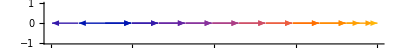

```mathematica
StreamPlot1D[x-1,{x,0,6}]
```

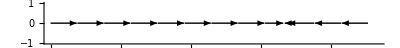

```mathematica
StreamPlot1D[x(1-x),{x,0,1.4},StreamStyle->Black,StreamColorFunction->None]
```

```mathematica
StreamPlot1D[x(1-x),{x,0,1.4},StreamStyle->Black,StreamColorFunction->None]/.Arrowheads[List[List[_,_]]]->Arrowheads[0.02]
```

-Graphics-

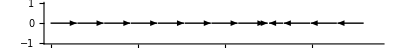

```mathematica
StreamPlot1D[x(1-x),{x,0,1.5},StreamStyle->Black,StreamColorFunction->None]
```

```mathematica
VectorPlot1D[func_,{x_,xmin_,xmax_},opts___?OptionQ]:=
Module[{streampoints,streamplotopts},
vectorplotopts=FilterRules[Flatten[{opts,Options[VectorPlot1D]}],Options[VectorPlot]];

VectorPlot[{func,0},{x,xmin,xmax},{y,-10^-8,10^-8},Evaluate[Sequence@@vectorplotopts]]
];
Options[VectorPlot1D]={VectorPoints->21,Frame->False,Axes->{True,False},AspectRatio->0.02};
```

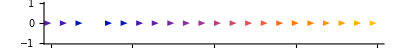

```mathematica
VectorPlot1D[x-1,{x,0,6},VectorPoints->21]/.Arrow[{{x1_,y1_},{x2_,y2_}}]->Arrow[{{x2-10^-8,y2},{x2,y2}}]
```

```mathematica
?ListVectorPlot
```

VectorPlot::vectsc: {None,Automatic,#5&} is not a valid VectorScale specification.

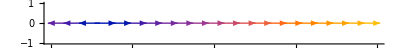

```mathematica
VectorPlot1D[x-1,{x,0,6},VectorPoints->21,VectorMarkers->Placed[Arrow,"End"],VectorScale->{None,Automatic}]
```

```mathematica
?Arrow
```

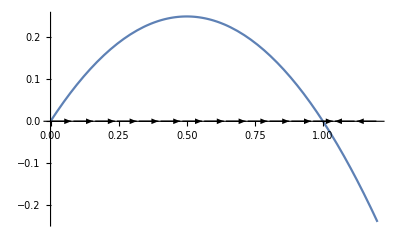

```mathematica
Show[
Plot[x(1-x),{x,0,1.2}],
VectorPlot1D[x(1-x),{x,0,1.2},VectorStyle->Black,VectorColorFunction->None,VectorPoints->15]
]
```

```mathematica
Placed[,"End"]]
```

```mathematica
VectorPlot1D[func_,{x_,xmin_,xmax_},opts___?OptionQ]:=
Module[{streampoints,streamplotopts},
vectorplotopts=FilterRules[Flatten[{opts,Options[VectorPlot1D]}],Options[VectorPlot]];

ListVectorPlot[Table[{{x,0},{func,0}},{x,xmin,xmax,(xmax-xmin)/(21)}],Evaluate[Sequence@@vectorplotopts]]
];
Options[VectorPlot1D]={VectorPoints->21,Frame->False,Axes->{True,False},AspectRatio->0.02};
```

```mathematica
VectorPlot1D[x(1-x),{x,0,1.2}]
```

ListVectorPlot::vfldata: {{{0.,0},{0.,0}},{{0.0571429,0},{0.0538776,0}},{{0.114286,0},{0.101224,0}},{{0.171429,0},{0.142041,0}},{«1»,{«20»,0}},«1»,{{«19»,0},«1»},{{0.4,0},{0.24,0}},{{0.457143,0},{0.248163,0}},{{0.514286,0},{0.249796,0}},«12»} is not a valid vector field dataset or a valid list of datasets.

ListVectorPlot[{{{0.,0},{0.,0}},{{0.0571429,0},{0.0538776,0}},{{0.114286,0},{0.101224,0}},{{0.171429,0},{0.142041,0}},{{0.228571,0},{0.176327,0}},{{0.285714,0},{0.204082,0}},{{0.342857,0},{0.225306,0}},{{0.4,0},{0.24,0}},{{0.457143,0},{0.248163,0}},{{0.514286,0},{0.249796,0}},{{0.571429,0},{0.244898,0}},{{0.628571,0},{0.233469,0}},{{0.685714,0},{0.21551,0}},{{0.742857,0},{0.19102,0}},{{0.8,0},{0.16,0}},{{0.857143,0},{0.122449,0}},{{0.914286,0},{0.0783673,0}},{{0.971429,0},{0.0277551,0}},{{1.02857,0},{-0.0293878,0}},{{1.08571,0},{-0.0930612,0}},{{1.14286,0},{-0.163265,0}},{{1.2,0},{-0.24,0}}},VectorPoints→21,Frame→False,Axes→{True,False},AspectRatio→0.02]

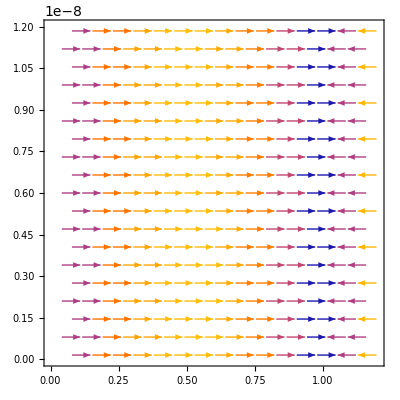

```mathematica
ListVectorPlot[Table[{{x,10^-8 x},{x(1-x),0}},{x,0,1.2,1.2/(11)}]]
```

```mathematica
data =Flatten[ Table[{{x,y},{y,-x}},{x,-3,3,1},{y,-3,3,1}],1]
```

{{{-3,-3},{-3,3}},{{-3,-2},{-2,3}},{{-3,-1},{-1,3}},{{-3,0},{0,3}},{{-3,1},{1,3}},{{-3,2},{2,3}},{{-3,3},{3,3}},{{-2,-3},{-3,2}},{{-2,-2},{-2,2}},{{-2,-1},{-1,2}},{{-2,0},{0,2}},{{-2,1},{1,2}},{{-2,2},{2,2}},{{-2,3},{3,2}},{{-1,-3},{-3,1}},{{-1,-2},{-2,1}},{{-1,-1},{-1,1}},{{-1,0},{0,1}},{{-1,1},{1,1}},{{-1,2},{2,1}},{{-1,3},{3,1}},{{0,-3},{-3,0}},{{0,-2},{-2,0}},{{0,-1},{-1,0}},{{0,0},{0,0}},{{0,1},{1,0}},{{0,2},{2,0}},{{0,3},{3,0}},{{1,-3},{-3,-1}},{{1,-2},{-2,-1}},{{1,-1},{-1,-1}},{{1,0},{0,-1}},{{1,1},{1,-1}},{{1,2},{2,-1}},{{1,3},{3,-1}},{{2,-3},{-3,-2}},{{2,-2},{-2,-2}},{{2,-1},{-1,-2}},{{2,0},{0,-2}},{{2,1},{1,-2}},{{2,2},{2,-2}},{{2,3},{3,-2}},{{3,-3},{-3,-3}},{{3,-2},{-2,-3}},{{3,-1},{-1,-3}},{{3,0},{0,-3}},{{3,1},{1,-3}},{{3,2},{2,-3}},{{3,3},{3,-3}}}

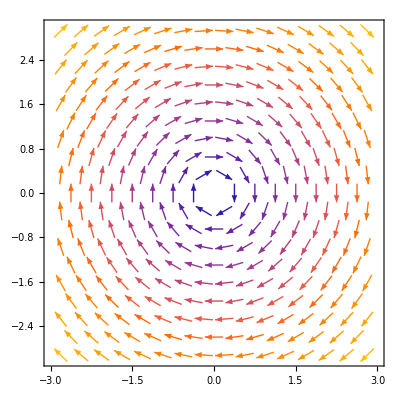

```mathematica
ListVectorPlot[data]
```

```mathematica
?Triangle
```

```mathematica
▶
```

▶

```mathematica
?NumberLinePlot
```

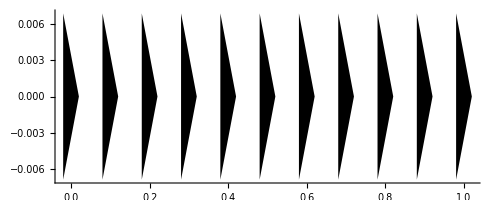

```mathematica
w=0.04;
h=0.016;
Show[
Graphics[Table[Triangle[{{x+w/2,0},{x-w/2,(h/2)Sqrt[3]/2},{x-w/2,-(h/2)Sqrt[3]/2}}],{x,0,1,0.1}]],
Axes->{True,False}
]
```

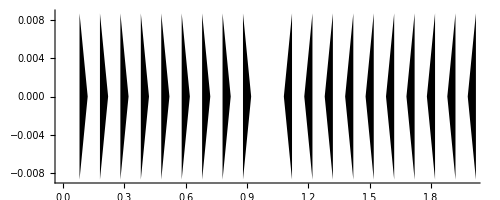

```mathematica
w=0.04;
h=0.02;
rt[x_]:=Triangle[{{x+w/2,0},{x-w/2,(h/2)Sqrt[3]/2},{x-w/2,-(h/2)Sqrt[3]/2}}];
lt[x_]:=Triangle[{{x-w/2,0},{x+w/2,(h/2)Sqrt[3]/2},{x+w/2,-(h/2)Sqrt[3]/2}}];
Show[
Graphics[Table[
Which[x(1-x)<0,lt[x],x(1-x)>0,rt[x]]
,{x,0,2,0.1}]],
Axes->{True,False},PlotRange->{{0,2},Automatic}
]
```

```mathematica
Clear[VectorPlot1D];
VectorPlot1D[func_,{var_,varmin_,varmax_},opts___?OptionQ]:=Module[{rt,lt,vectorpoints},
vectorpoints=Evaluate[VectorPoints/.Flatten[{opts,Options[VectorPlot1D]}]];
rt[x_]:=Triangle[{{x+w/2,0},{x-w/2,(h/2)Sqrt[3]/2},{x-w/2,-(h/2)Sqrt[3]/2}}];
lt[x_]:=Triangle[{{x-w/2,0},{x+w/2,(h/2)Sqrt[3]/2},{x+w/2,-(h/2)Sqrt[3]/2}}];
Show[
Graphics[Table[
Which[func<0,lt[var],func>0,rt[var]]
,{var,varmin,varmax,(varmax-varmin)/vectorpoints}]],
Axes->{True,False},PlotRange->{{0,2},Automatic}
]
];
Options[VectorPlot1D]={VectorPoints->21};
```

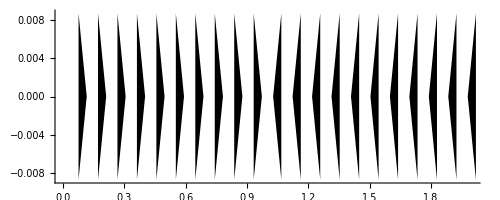

```mathematica
VectorPlot1D[x(1-x),{x,0,2},PlotPoints->11]
```

```mathematica
Clear[VectorPlot1D];
VectorPlot1D[func_,{var_,varmin_,varmax_},opts___?OptionQ]:=Module[{
vectorpoints,markerwidth,markeraspectratio,markerspacing,
rt,lt,varrange,w,h},

vectorpoints=Evaluate[VectorPoints/.Flatten[{opts,Options[VectorPlot1D]}]];
markerwidth=Evaluate[MarkerWidth/.Flatten[{opts,Options[VectorPlot1D]}]];
If[markerwidth==Automatic,markerwidth=varrange/vectorpoints];
markeraspectratio=Evaluate[MarkerAspectRatio/.Flatten[{opts,Options[VectorPlot1D]}]];
markerspacing=Evaluate[MarkerSpacing/.Flatten[{opts,Options[VectorPlot1D]}]];

varrange=varmax-varmin;
w=(1-markerspacing)markerwidth;
h=w*markeraspectratio;

(*Print[{w,h}];*)

rt[x_]:=Triangle[{{x+w/2,0},{x-w/2,(h/2)Sqrt[3]/2},{x-w/2,-(h/2)Sqrt[3]/2}}];
lt[x_]:=Triangle[{{x-w/2,0},{x+w/2,(h/2)Sqrt[3]/2},{x+w/2,-(h/2)Sqrt[3]/2}}];

Show[
Graphics[Table[
Which[
(func/.var->x)<0&&(func/.var->x-w/2)<0&&(func/.var->x+w/2)<0,lt[var],
(func/.var->x)>0&&(func/.var->x-w/2)>0&&(func/.var->x+w/2)>0,rt[var]
],{x,varmin,varmax,varrange/vectorpoints}]],
Axes->{True,False}
]
];
Options[VectorPlot1D]={VectorPoints->21,MarkerWidth->Automatic,MarkerAspectRatio->0.5,MarkerSpacing->0.5};
```

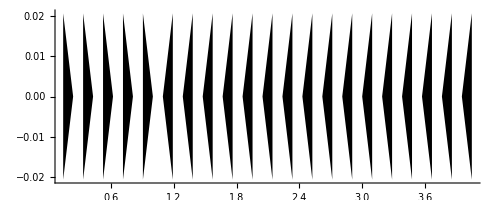

```mathematica
VectorPlot1D[x(1-x),{x,0,4}]
```

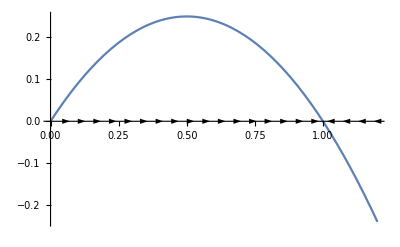

```mathematica
Show[
Plot[x(1-x),{x,0,1.2}],
VectorPlot1D[x(1-x),{x,0,1.2}]
]
```

```mathematica
EcoPhasePortrait[]
```

```mathematica
PIP[]
```

```mathematica
MIP[]
```

```mathematica
PairwiseInvasibilityPlot[]
```

```mathematica
PlotEcoPhasePortrait[]
```

```mathematica
PlotInv[]
```

```mathematica
PlotEcoPhaseSpace[]
```